```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY201/sec_int_data/368nm.dat"]
```

{{1.59376,-0.891232},{1.5163,-0.847278},{1.45822,-0.814682},{1.41492,-0.841902},{1.36475,-0.799019},{1.33366,-0.758796},{1.2821,-0.732845},{1.25075,-0.719286},{1.2275,-0.727635},{1.20277,-0.708708},{1.18632,-0.683969},{1.16701,-0.717522},{1.14926,-0.743809},{1.12973,-0.901156},{1.10588,-inf},{1.11907,-0.932928},{1.13878,-0.815722},{1.30525,-0.812471},{1.35407,-0.920349}}

0.229416 (-0.334101+2.85578 -inf)+0.178327 (-2.9799-2.64184 -inf) x

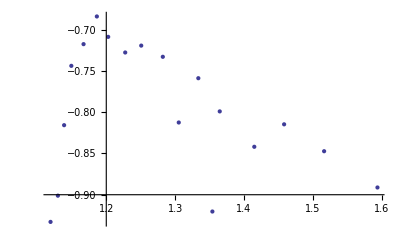

-Graphics-

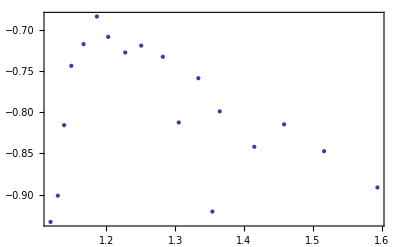

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```